This notebook contains a simulation of an uncontrolled inverted pendulum on a cart.

Import dependencies

```mathematica
AppendTo[$Path,NotebookDirectory[]];
```

```mathematica
<<draw_inverted_pendulum.m;
```

Define constants

```mathematica
(* Acceleration due to gravity in m/s^2 *)
g=9.8;
```

```mathematica
(* The length of the pendulum in m *)
l=0.43;
```

```mathematica
(* The mass of the cart in kg *)
m1=0.103;
```

```mathematica
(* The mass of the pendulum in kg *)
m2=0.066;
```

```mathematica
(* The duration of the simulation in s *)
tMax=5;
```

Define initial conditions

```mathematica
(* The initial angle of the pendulum in rad *)
θ0=Pi/6;
```

```mathematica
(* The initial angular velocity of the pendulum in rad/s *)
ω0=0;
```

```mathematica
(* The initial x position of the cart in m *)
x0=0;
```

```mathematica
(* The initial x velocity of the cart in m/s *)
v0=0;
```

Solve the equations of motion

```mathematica
{fθ,fx}=NDSolveValue[
{
θ[0]==θ0,
θ'[0]==ω0,
θ''[t]==((m1+m2)g Sin[θ[t]]-m2 l θ'[t]^2Cos[θ[t]]Sin[θ[t]])/(l(m1+m2)-m2 l Cos[θ[t]]^2),
x[0]==x0,
x'[0]==v0,
x''[t]==(m2 g Sin[2θ[t]]-2m2 l θ'[t]^2Sin[θ[t]])/(2m1+m2-m2 Cos[2θ[t]])
},
{θ,x},
{t,0,tMax}
];
```

Generate a plot

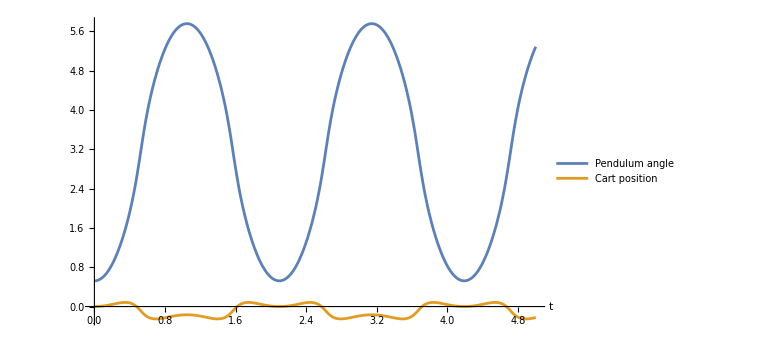

```mathematica
plot=Plot[{fθ[t],fx[t]},{t,0,tMax},AxesLabel->{t},ImageSize->Large,PlotLegends->{"Pendulum angle","Cart position"}]
```

Uncomment to export a PNG of the plot

```mathematica
(*Export[FileNameJoin[{NotebookDirectory[],"uncontrolled.png"}],plot]; *)
```

Generate an animation

```mathematica
Animate[
drawInvertedPendulum[l,fθ[t],fx[t]],
{t,0,tMax},
DefaultDuration->tMax
]
```

Uncomment to export a GIF of the animation

```mathematica
(*Export[
FileNameJoin[{NotebookDirectory[],"uncontrolled.gif"}],
Table[drawInvertedPendulum[l, fθ[t],fx[t]],{t,0,tMax,1/24}],DisplayDurations->1/24
]; *)
```